## Random Functions

```mathematica
ClearAll["Global`*"]
```

```mathematica
Rainbow := Table[ColorData["Rainbow",i/(Length[functions]-1)],{i,0,Length[functions]-1}]
```

## Modulation Instability

```mathematica
Ψ[t_,ρ_]:= ρ*ⅇ^(ⅈ*ρ^2*t)
```

```mathematica
g[q_,ρ_]:=Im[Abs[q]*√(q^2-2*ρ^2)]
```

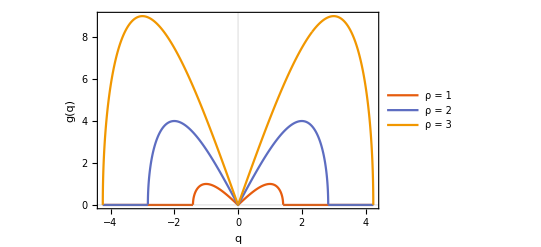

modulationinstabilitygain.png

```mathematica
functions:=Table[magψ[x,0, 1,ϕ],{ϕ,0,π/4+0.5,π/16}]
imagem = Plot[Evaluate[Table[g[q,ρ],{ρ,1,3}]],{q,-3 √2,+3 √2}
,PlotTheme->"Scientific"
, PlotRange->Automatic
, Background->White
,FrameLabel->{Style["q",Bold,16],Style["g(q)",Bold,16]}
,PlotPoints->10000
,PlotLegends->Table[StringForm["ρ = ``",i],{i,1,3}]
]
Export["modulationinstabilitygain.png",imagem]
```

```mathematica
SystemOpen["modulationinstabilitygain.png"]
```

## Dark Solitons

```mathematica
ψdark[x_,t_,Ω_]:=√Ω*Tanh[√(Ω/2)*x]*ⅇ^(-ⅈ *Ω *t)
```

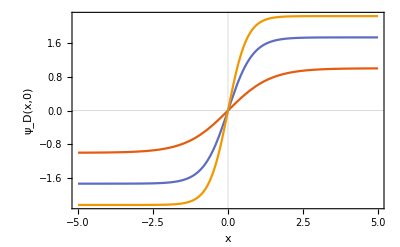

darksolitonprofile.png

```mathematica
functions1:=Table[ψdark[x,0,Ω],{Ω,1,5,2}]
imagem1 = Plot[Evaluate[functions1],{x,-5,5}
,PlotTheme->"Scientific"
,FrameLabel->{Style["x",Bold,16],Style["ψ_D(x,0)",Bold,16]}
]
Export["darksolitonprofile.png",imagem1]
```

```mathematica
ψdarkmag[x_,Ω_]:=Ω*Tanh[√(Ω/2)*x]^2
```

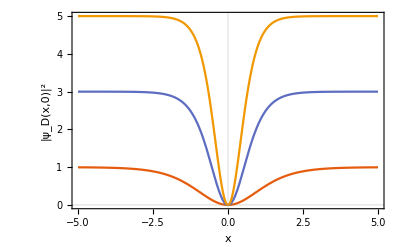

darksolitonabs.png

```mathematica
functions:=Table[ψdarkmag[x,Ω],{Ω,1,5,2}]
imagem3 = Plot[Evaluate[functions],{x,-5,5}
,PlotTheme->"Scientific"
, PlotRange->Automatic
,FrameLabel->{Style["x",Bold,16],Style["|ψ_D(x,0)|^2",Bold,16]}
]
Export["darksolitonabs.png",imagem3]
```

```mathematica
imagem3D = Plot3D[ψdarkmag[x, 1],{x,-20,20},{t,0,20}
,PlotTheme->"Scientific"
,PlotRange->{0,1}
,AxesLabel->{Style["x",Bold,16],Style["t",Bold,16]},PlotLabel->Style["|ψ_D(x,t)|^2",Bold,16]
,Boxed->False
,ColorFunction->ColorData["GrayTones"]
,PerformanceGoal->"Quality"
,PlotPoints-> 300
]
Export["darksoliton3D.png",imagem3D,"PNG"]
```

-Graphics3D-

darksoliton3D.png

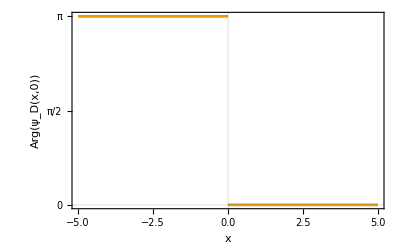

darksolitonphase.png

```mathematica
functions2:=Table[Arg[ψdark[x,0,Ω]],{Ω,1,5,2}]
imagem2 = Plot[Evaluate[functions2], {x,-5,5}
,PlotTheme->"Scientific"
,FrameTicks->{ {Subdivide[0,Pi,2],None},Automatic}
,FrameLabel->{Style["x",Bold,16],Style["Arg(ψ_D(x,0))",Bold,16]}
]
Export["darksolitonphase.png",imagem2]
```

Soliton width L dependence on Ω

```mathematica
L[Ω_]:=√(2/Ω)
```

```mathematica
cores:={Red,Red,Blue,Blue,Orange}
```

```mathematica
pontos:=Table[{cores[[Ω]],PointSize@Large,Point[{{Ω,L[Ω]}}]},{Ω,1,5,2}]
```

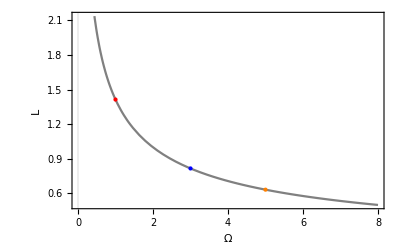

darksolitonwidth.png

```mathematica
imagem6 = Plot[L[Ω],{Ω,0,8}
,Epilog->pontos
, PlotTheme->"Scientific"
, PlotStyle->Gray
,FrameLabel->{Style["Ω",Bold,16],Style["L",Bold,16]}
]
Export["darksolitonwidth.png",imagem6]
```

## Grey Solitons

```mathematica
ψgray[x_,t_, Ω_, θ_]:=√Ω*Exp[-ⅈ*Ω*t]*(ⅈ*Sin[θ] + Cos[θ]*Tanh[√(Ω/2)Cos[θ](x-√(2Ω)*Sin[θ]*t)])
```

```mathematica
ψgraymag[x_,t_, Ω_, θ_] := Ω*( Sin[θ]^2 + Cos[θ]^2*Tanh[√(Ω/2)Cos[θ](x-√(2Ω)*Sin[θ]*t)]^2)
```

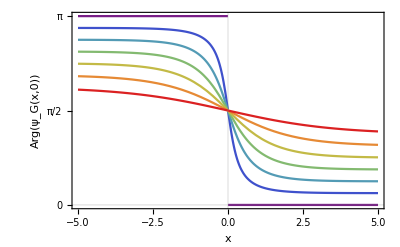

graysolitonphase.png

```mathematica
functions:=Table[Arg[ψgray[x,0,1,θ]],{θ,0,π/4+0.5,π/16}]
imagem2 = Plot[Evaluate[functions], {x,-5,5}
,PlotTheme->"Scientific"
, PlotStyle->Rainbow
,FrameTicks->{ {Subdivide[0,Pi,2],None},Automatic}
,FrameLabel->{Style["x",Bold,16],Style["Arg(ψ_G(x,0))",Bold,16]}
]
Export["graysolitonphase.png",imagem2]
```

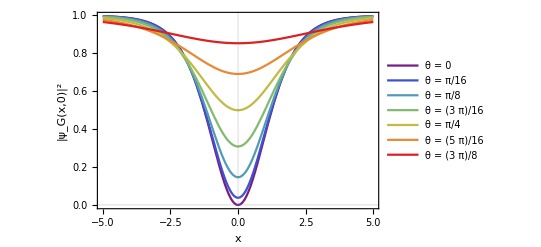

graysolitonabs.png

```mathematica
functions:=Table[ψgraymag[x,0, 1,θ],{θ,0,π/4+0.5,π/16}]
imagem = Plot[Evaluate[functions],{x,-5,5}
,PlotTheme->"Scientific"
, PlotRange->Automatic
, PlotStyle->Rainbow
,FrameLabel->{Style["x",Bold,16],Style["|ψ_G(x,0)|^2",Bold,16]}
,PlotLegends->Table[StringForm["θ = ``",i],{i,0,π/4+0.5,π/16}]
]
Export["graysolitonabs.png",imagem]
```

```mathematica
imagem3D = Plot3D[ψgraymag[x,t, 1, 0],{x,-30,30},{t,0,20}
,PlotTheme->"Scientific"
,PlotRange->{0,1}
,AxesLabel->{Style["x",Bold,16],Style["t",Bold,16]},PlotLabel->Style["|ψ_G(x,t)|^2",Bold,16]
,Boxed->False
,Mesh->5
,ColorFunction->ColorData["GrayTones"]
,PerformanceGoal->"Quality"
,PlotPoints-> 300
]
Export["graysoliton3D.png",imagem3D]
```

-Graphics3D-

graysoliton3D.png

## Akhmediev and Kuznetsov - Ma Breather

```mathematica
β[a_] :=√(2*(1-2a)) 
α[a_] := 2*√a*β[a]
```

```mathematica
ψBreather[x_,t_,a_]:= Exp[ⅈ*t](1+(β[a]^2*Cosh[α[a]*t]+ⅈ*α[a]*Sinh[α[a]*t])/(√(2*a)*Cos[β[a]*x]-Cosh[α[a]*t]))
```

```mathematica
ψBreatherAmp[x_,t_,a_]:= (1+(β[a]^2*Cosh[α[a]*t]+ⅈ*α[a]*Sinh[α[a]*t])/(√(2*a)*Cos[β[a]*x]-Cosh[α[a]*t]))(1+(β[a]^2*Cosh[α[a]*t]-ⅈ*α[a]*Sinh[α[a]*t])/(√(2*a)*Cos[β[a]*x]-Cosh[α[a]*t]))
```

```mathematica
imagem3D = Plot3D[ψBreatherAmp[x,t,0.25],{x,-10,10},{t,-5,5}
,PlotTheme->"Scientific"
,PlotRange-> Full
,AxesLabel->{Style["x",Bold,16],Style["t",Bold,16]},PlotLabel->Style["|ψ_A(x,t)|^2",Bold,16]
,ColorFunction-> ColorData["TemperatureMap"]
,PerformanceGoal->"Quality"
,Boxed->False
,PlotPoints-> 300
]
```

-Graphics3D-

```mathematica
imagem3D = Plot3D[ψBreatherAmp[x,t,2],{x,-5,5},{t,-5,5}
,PlotTheme->"Scientific"
,PlotRange-> Full
,AxesLabel->{Style["x",Bold,16],Style["t",Bold,16]},PlotLabel->Style["|ψ_KM(x,t)|^2",Bold,16]
,ColorFunction-> ColorData["TemperatureMap"]
,PerformanceGoal->"Quality"
,Boxed->False
,PlotPoints-> 300
]
```

-Graphics3D-

```mathematica
AmpMaxAkh[a_]:=(1+(2(1-2a))/(√(2a)-1))^2
```

```mathematica
N[AmpMaxAkh[0.00001]]
```

1.01797

```mathematica
AmpMaxKM[a_]:=(1-(2(2a-1))/(√(2a)-1))^2
```

```mathematica
N[AmpMaxKM[0.8]]
```

12.4596

```mathematica
ωKM[a_]:=((√(2(2a-1)))/(2π))^-1
```

```mathematica
f = N[ωKM[2]]
```

2.5651

```mathematica
10/f
```

3.89848

## Peregrine Soliton

```mathematica
ψPeregrine[x_,t_]:=Exp[ⅈ*t](1-4*(1+2*ⅈ*t)/(1+2*x^2+4*t^2))
```

```mathematica
ψPeregrineAmp[x_,t_] := (1-4*(1+2*ⅈ*t)/(1+2*x^2+4*t^2))(1-4*(1+2*-ⅈ*t)/(1+2*x^2+4*t^2))
```

```mathematica
imagem3D = Plot3D[ψPeregrineAmp[x,t],{x,-5,5},{t,-5,5}
,PlotTheme->"Scientific"
,PlotRange-> Full
,AxesLabel->{Style["x",Bold,16],Style["t",Bold,16]},PlotLabel->Style["|ψ_P(x,t)|^2",Bold,16]
,Boxed->False
,ColorFunction-> ColorData["TemperatureMap"]
,PerformanceGoal->"Quality"
,PlotPoints-> 300
]
Export["perigrinesoliton3D.png",imagem3D]
```

-Graphics3D-

perigrinesoliton3D.png